```mathematica
Clear["Global`*"]
```

```mathematica
esing[u_]:=(ec+f) uc/u+f ((1-uc/u)^τ-1)
```

```mathematica
ai={-1/√2,-1/√2,-1.5411,-4.30479,-13.6579,-46.8554,-169.493,-637.078};
```

```mathematica
ept[u_]=Sum[ai[[n]]/u^n,{n,1,8}];
```

```mathematica
qi=Table[{i,ai[[i]]/ai[[i-1]]},{i,3,8}];
```

```mathematica
fit=NonlinearModelFit[qi,uc (1-(τ+1)/n),{uc,τ},n];
```

```mathematica
fit["BestFitParameters"]
```

{uc→4.69726,τ→0.613701}

```mathematica
a[n_]:=a[n-1] fit["Function"][n]
a[2]=ai[[2]];
```

```mathematica
nmax=100;
eextr[u_]=ai[[1]]/u+ai[[2]]/u^2+Sum[a[n]/u^n,{n,3,nmax}];
```

```mathematica
fit2=NonlinearModelFit[Table[{u,eextr[u]},{u,uc/.fit["BestFitParameters"],10,.1}],esing[u]/.fit["BestFitParameters"],{ec,f},u];
```

```mathematica
fit2["BestFitParameters"]
```

{ec→-0.252495,f→0.260348}

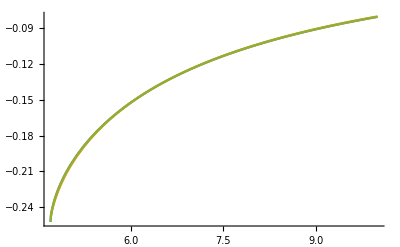

```mathematica
Plot[{esing[u]/.fit["BestFitParameters"]/.fit2["BestFitParameters"],eextr[u],fit2["Function"][u]},{u,uc/.fit["BestFitParameters"],10}]
```

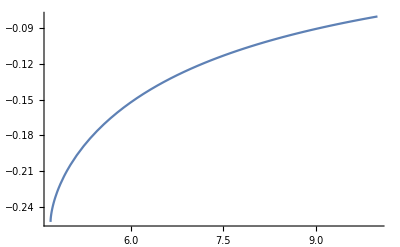

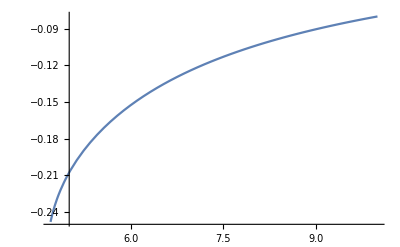

-Graphics-

```mathematica
Plot[esing[u]/.fit["BestFitParameters"]/.fit2["BestFitParameters"],{u,uc/.fit["BestFitParameters"],10}]
Plot[eextr[u],{u,uc/.fit["BestFitParameters"],10}]
Plot[fit2["Function"][u],{u,uc/.fit["BestFitParameters"],10}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
spectrum=Import["spectrum.dat"];
```

```mathematica
fit=NonlinearModelFit[spectrum,a1 Exp[-b1 (ω-ω01)^2]+a2 Exp[-b2 (ω-ω02)^2],{a1,b1,a2,b2,ω01,ω02},ω];
```

```mathematica
fit["BestFitParameters"]
```

{a1→0.996306,b1→0.535754,a2→0.512187,b2→2.07903,ω01→2.99786,ω02→5.48399}

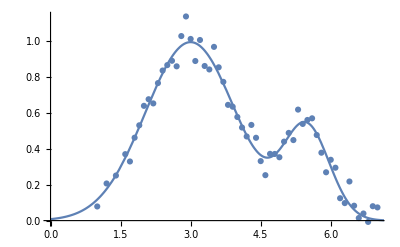

```mathematica
Show[ListPlot[spectrum],Plot[fit["Function"][ω],{ω,0,8}]]
```